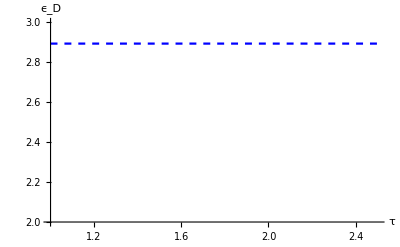

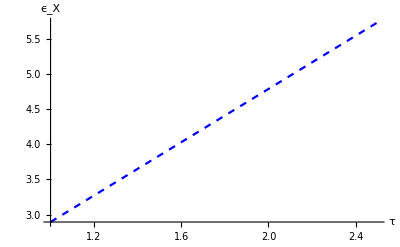

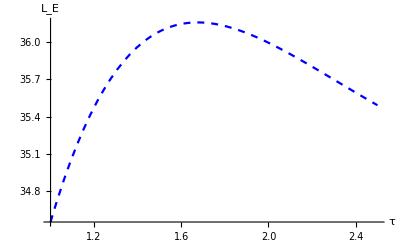

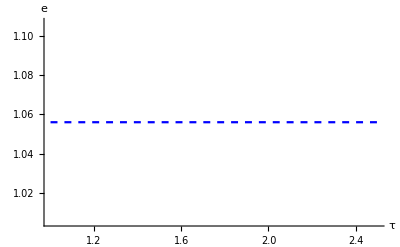

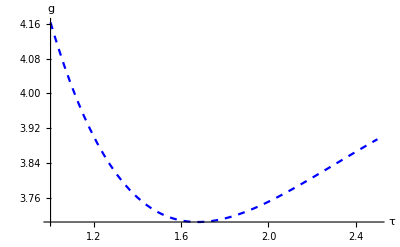

-Graphics-

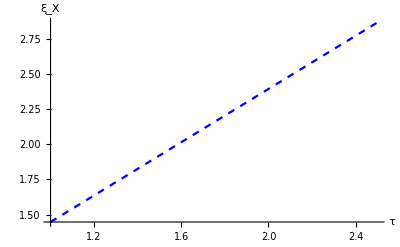

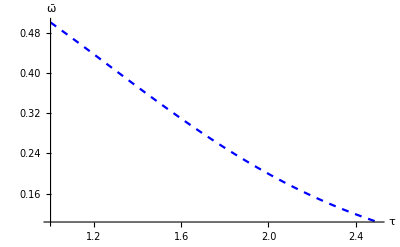

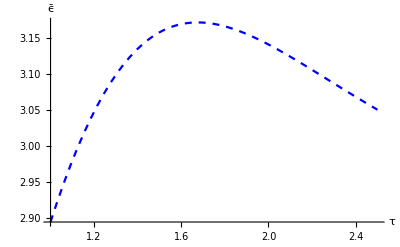

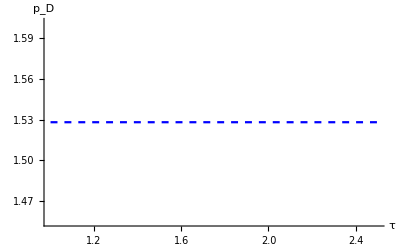

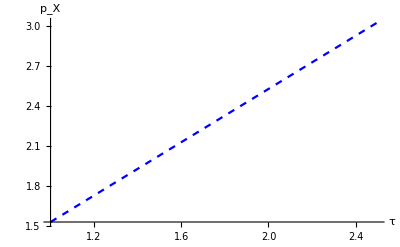

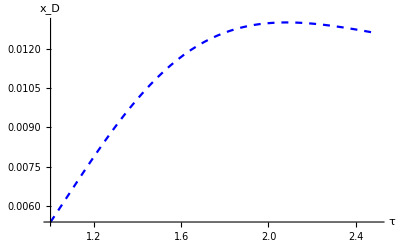

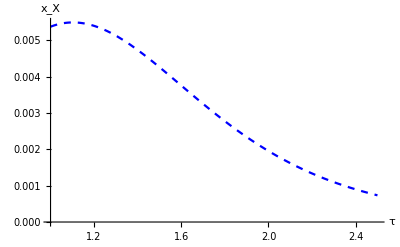

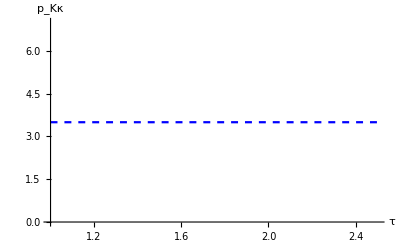

```mathematica
(*This file simulates how the exponent model with Grossman-Helpman specification of p_K responds to the change of trade costs.*)
v[x_]=Exp[-b x];
ϵ[x_]=-(x v''[x])/v'[x];
Subscript[ϵ, D]=ϵ[Subscript[ξ, D]];
Subscript[ϵ, X]=ϵ[Subscript[ξ, X]];
parameters={κ->7,ρ->0.8,w->1,L->50,δ->0.25,ψ->1,b->2,γ-> 1};
eqn1=Subscript[ξ, D] (1-1/Subscript[ϵ, D])τ-Subscript[ξ, X](1-1/Subscript[ϵ, X])==0;
eqn2=1/(ε̃)-(1-ω̃)1/Subscript[ϵ, D]-ω̃ 1/Subscript[ϵ, X]==0;
eqn3=g+δ-(w L (1+ψ))/κ(1-(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]]))==0;
eqn4=g-(w L (1+ψ))/(κ ε̃)+(ρ(ε̃-1))/(ε̃)+δ==0;
eqn5= ω̃-(Subscript[ξ, X] v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])==0;
eqn6= e Subscript[ξ, X](1-1/Subscript[ϵ, X])-τ w==0;
eqn7 =Le (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])-L(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])==0; 
neweqn1L=eqn1/.parameters;
neweqn2L=eqn2/.parameters;
neweqn3L=eqn3/.parameters;
neweqn4L=eqn4/.parameters;
neweqn5L=eqn5/.parameters;
neweqn6L=eqn6/.parameters;
neweqn7L=eqn7/.parameters;
Nvalue=Exp[g] /.parameters;(*we normalize N0=1, and consider t=1 *)
muvalue=Exp[g] (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]] );(*we normalize N0=1, and consider t=1 *)
expotauGH1=Plot[Subscript[ϵ, D]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotRange->{{1,2.5},{2,3}},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ϵ_D" }]
expotauGH2=Plot[Subscript[ϵ, X]/.parameters/.
FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ϵ_X" }]
expotauGH3=Plot[Le/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"L_E" }]
expotauGH4=Plot[e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"e" }]
expotauGH5=Plot[g/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"g" }]
expotauGH6=Plot[Subscript[ξ, D]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ξ_D" }]
expotauGH7=Plot[Subscript[ξ, X]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ξ_X" }]
expotauGH8=Plot[ω̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ω̄" }]
expotauGH9=Plot[ε̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"ϵ̄" }]
expotauGH10=Plot[Subscript[ξ, D] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"p_D" }]
expotauGH11=Plot[Subscript[ξ, X] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"p_X" }]
expotauGH12=Plot[v'[Subscript[ξ, D]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"x_D"}]
expotauGH13=Plot[v'[Subscript[ξ, X]]/muvalue/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"x_X"} ]
expotauGH14=Plot[κ/(1+ψ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,"p_Kκ"}]
expotauGH15=Plot[1/ρ(Log[v[Subscript[ξ, D]]+v[Subscript[ξ, X]]]+ g/ρ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,2.5},PlotStyle-> {Blue,Dashed},AxesLabel-> {τ,Welfare} ]
```

```mathematica
allexpotauGH={{expotauGH1,expotauGH2,expotauGH3,expotauGH4},{expotauGH5,expotauGH6,expotauGH7,expotauGH8},{expotauGH9,expotauGH10,expotauGH11,expotauGH12},{expotauGH13,expotauGH14,expotauGH15}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}